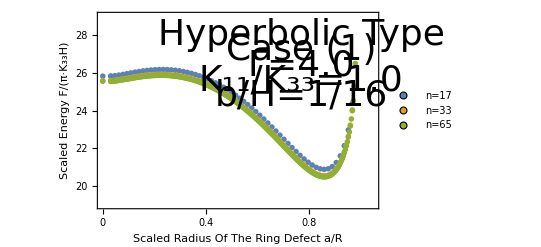

```mathematica
a=
{{0,25.821661},{0.125000,25.820405},{0.125000,25.820405},{0.187500,25.844939},
{0.250000,25.877197},{0.312500,25.914273},{0.375000,25.953552},{0.437500,25.993004},
{0.500000,26.031020},{0.562500,26.066299},{0.625000,26.097777},{0.687500,26.124574},
{0.750000,26.145965},{0.812500,26.161344},{0.875000,26.170210},{0.937500,26.172144},
{1.000000,26.166797},{1.062500,26.153879},{1.125000,26.133147},{1.187500,26.104400},
{1.250000,26.067470},{1.312500,26.022218},{1.375000,25.968529},{1.437500,25.906310},
{1.500000,25.835487},{1.562500,25.756004},{1.625000,25.667820},{1.687500,25.570913},
{1.750000,25.465274},{1.812500,25.350914},{1.875000,25.227861},{1.937500,25.096164},
{2.000000,24.955898},{2.062500,24.807164},{2.125000,24.650096},{2.187500,24.484870},
{2.250000,24.311705},{2.312500,24.130882},{2.375000,23.942747},{2.437500,23.747731},
{2.500000,23.546367},{2.562500,23.339310},{2.625000,23.127365},{2.687500,22.911518},
{2.750000,22.692975},{2.812500,22.473209},{2.875000,22.254015},{2.937500,22.037580},
{3.000000,21.826562},{3.062500,21.624191},{3.125000,21.434394},{3.187500,21.261934},
{3.250000,21.112607},{3.312500,20.993475},{3.375000,20.913188},{3.437500,20.882438},
{3.500000,20.914642},{3.562500,21.027072},{3.625000,21.242918},{3.687500,21.595510},
{3.750000,22.138386},{3.812500,22.975277},{3.875000,24.387527}};
b=a*Table[{0.25,1},{i,0,62}];
a2=
{{0,25.584623},{0.125000,25.580156},{0.125000,25.580156},{0.156250,25.589402},
{0.187500,25.601422},{0.218750,25.615621},{0.250000,25.631486},{0.281250,25.648591},
{0.312500,25.666572},{0.343750,25.685115},{0.375000,25.703948},{0.406250,25.722828},
{0.437500,25.741543},{0.468750,25.759901},{0.500000,25.777731},{0.531250,25.794877},
{0.562500,25.811200},{0.593750,25.826572},{0.625000,25.840878},{0.656250,25.854014},
{0.687500,25.865885},{0.718750,25.876402},{0.750000,25.885487},{0.781250,25.893069},
{0.812500,25.899081},{0.843750,25.903463},{0.875000,25.906160},{0.906250,25.907123},
{0.937500,25.906306},{0.968750,25.903668},{1.000000,25.899170},{1.031250,25.892777},
{1.062500,25.884459},{1.093750,25.874186},{1.125000,25.861932},{1.156250,25.847672},
{1.187500,25.831386},{1.218750,25.813052},{1.250000,25.792653},{1.281250,25.770172},
{1.312500,25.745593},{1.343750,25.718904},{1.375000,25.690092},{1.406250,25.659146},
{1.437500,25.626056},{1.468750,25.590813},{1.500000,25.553410},{1.531250,25.513840},
{1.562500,25.472097},{1.593750,25.428177},{1.625000,25.382076},{1.656250,25.333792},
{1.687500,25.283322},{1.718750,25.230667},{1.750000,25.175826},{1.781250,25.118802},
{1.812500,25.059596},{1.843750,24.998214},{1.875000,24.934659},{1.906250,24.868939},
{1.937500,24.801062},{1.968750,24.731037},{2.000000,24.658876},{2.031250,24.584592},
{2.062500,24.508200},{2.093750,24.429717},{2.125000,24.349164},{2.156250,24.266564},
{2.187500,24.181941},{2.218750,24.095324},{2.250000,24.006746},{2.281250,23.916242},
{2.312500,23.823854},{2.343750,23.729626},{2.375000,23.633608},{2.406250,23.535858},
{2.437500,23.436436},{2.468750,23.335412},{2.500000,23.232865},{2.531250,23.128878},
{2.562500,23.023547},{2.593750,22.916977},{2.625000,22.809286},{2.656250,22.700602},
{2.687500,22.591068},{2.718750,22.480844},{2.750000,22.370103},{2.781250,22.259041},
{2.812500,22.147872},{2.843750,22.036832},{2.875000,21.926183},{2.906250,21.816215},
{2.937500,21.707247},{2.968750,21.599630},{3.000000,21.493753},{3.031250,21.390046},
{3.062500,21.288980},{3.093750,21.191077},{3.125000,21.096910},{3.156250,21.007114},
{3.187500,20.922386},{3.218750,20.843496},{3.250000,20.771293},{3.281250,20.706715},
{3.312500,20.650796},{3.343750,20.604683},{3.375000,20.569649},{3.406250,20.547107},
{3.437500,20.538636},{3.468750,20.546009},{3.500000,20.571228},{3.531250,20.616575},
{3.562500,20.684679},{3.593750,20.778612},{3.625000,20.902028},{3.656250,21.059376},
{3.687500,21.256223},{3.718750,21.499788},{3.750000,21.799871},{3.781250,22.170563},
{3.812500,22.633800},{3.843750,23.227853},{3.875000,24.033031},{3.906250,25.286865}};
b2=a2*Table[{0.25,1},{i,0,123}];
a3={{0,25.551374},{0.125000,25.546446},{0.125000,25.546446},{0.140625,25.550481},{0.156250,25.555334},{0.171875,25.560908},{0.187500,25.567115},{0.203125,25.573876},{0.218750,25.581121},{0.234375,25.588788},{0.250000,25.596819},{0.265625,25.605163},{0.281250,25.613771},{0.296875,25.622600},{0.312500,25.631609},{0.328125,25.640759},{0.343750,25.650015},{0.359375,25.659344},{0.375000,25.668715},{0.390625,25.678098},{0.406250,25.687467},{0.421875,25.696794},{0.437500,25.706055},{0.453125,25.715228},{0.468750,25.724289},{0.484375,25.733218},{0.500000,25.741996},{0.515625,25.750603},{0.531250,25.759020},{0.546875,25.767233},{0.562500,25.775223},{0.578125,25.782975},{0.593750,25.790475},{0.609375,25.797709},{0.625000,25.804663},{0.640625,25.811324},{0.656250,25.817680},{0.671875,25.823720},{0.687500,25.829432},{0.703125,25.834807},{0.718750,25.839832},{0.734375,25.844500},{0.750000,25.848800},{0.765625,25.852725},{0.781250,25.856265},{0.796875,25.859412},{0.812500,25.862159},{0.828125,25.864499},{0.843750,25.866425},{0.859375,25.867929},{0.875000,25.869005},{0.890625,25.869648},{0.906250,25.869851},{0.921875,25.869610},{0.937500,25.868918},{0.953125,25.867770},{0.968750,25.866162},{0.984375,25.864089},{1.000000,25.861547},{1.015625,25.858531},{1.031250,25.855038},{1.046875,25.851063},{1.062500,25.846602},{1.078125,25.841653},{1.093750,25.836212},{1.109375,25.830275},{1.125000,25.823840},{1.140625,25.816904},{1.156250,25.809463},{1.171875,25.801516},{1.187500,25.793059},{1.203125,25.784090},{1.218750,25.774607},{1.234375,25.764608},{1.250000,25.754090},{1.265625,25.743052},{1.281250,25.731491},{1.296875,25.719405},{1.312500,25.706794},{1.328125,25.693654},{1.343750,25.679986},{1.359375,25.665786},{1.375000,25.651055},{1.390625,25.635789},{1.406250,25.619989},{1.421875,25.603653},{1.437500,25.586779},{1.453125,25.569368},{1.468750,25.551417},{1.484375,25.532925},{1.500000,25.513893},{1.515625,25.494319},{1.531250,25.474202},{1.546875,25.453542},{1.562500,25.432338},{1.578125,25.410590},{1.593750,25.388296},{1.609375,25.365458},{1.625000,25.342073},{1.640625,25.318143},{1.656250,25.293666},{1.671875,25.268643},{1.687500,25.243073},{1.703125,25.216957},{1.718750,25.190294},{1.734375,25.163084},{1.750000,25.135329},{1.765625,25.107027},{1.781250,25.078179},{1.796875,25.048786},{1.812500,25.018847},{1.828125,24.988364},{1.843750,24.957337},{1.859375,24.925767},{1.875000,24.893655},{1.890625,24.861001},{1.906250,24.827806},{1.921875,24.794071},{1.937500,24.759798},{1.953125,24.724988},{1.968750,24.689642},{1.984375,24.653761},{2.000000,24.617348},{2.015625,24.580403},{2.031250,24.542930},{2.046875,24.504928},{2.062500,24.466402},{2.078125,24.427352},{2.093750,24.387782},{2.109375,24.347694},{2.125000,24.307090},{2.140625,24.265974},{2.156250,24.224348},{2.171875,24.182216},{2.187500,24.139582},{2.203125,24.096448},{2.218750,24.052820},{2.234375,24.008700},{2.250000,23.964094},{2.265625,23.919006},{2.281250,23.873441},{2.296875,23.827403},{2.312500,23.780900},{2.328125,23.733935},{2.343750,23.686516},{2.359375,23.638649},{2.375000,23.590340},{2.390625,23.541598},{2.406250,23.492428},{2.421875,23.442840},{2.437500,23.392842},{2.453125,23.342442},{2.468750,23.291650},{2.484375,23.240476},{2.500000,23.188931},{2.515625,23.137025},{2.531250,23.084769},{2.546875,23.032176},{2.562500,22.979259},{2.578125,22.926032},{2.593750,22.872507},{2.609375,22.818702},{2.625000,22.764630},{2.640625,22.710308},{2.656250,22.655755},{2.671875,22.600989},{2.687500,22.546028},{2.703125,22.490893},{2.718750,22.435606},{2.734375,22.380188},{2.750000,22.324665},{2.765625,22.269059},{2.781250,22.213398},{2.796875,22.157710},{2.812500,22.102022},{2.828125,22.046366},{2.843750,21.990773},{2.859375,21.935277},{2.875000,21.879913},{2.890625,21.824719},{2.906250,21.769733},{2.921875,21.714996},{2.937500,21.660552},{2.953125,21.606446},{2.968750,21.552724},{2.984375,21.499438},{3.000000,21.446639},{3.015625,21.394383},{3.031250,21.342727},{3.046875,21.291732},{3.062500,21.241462},{3.078125,21.191984},{3.093750,21.143368},{3.109375,21.095687},{3.125000,21.049021},{3.140625,21.003448},{3.156250,20.959056},{3.171875,20.915934},{3.187500,20.874176},{3.203125,20.833881},{3.218750,20.795152},{3.234375,20.758100},{3.250000,20.722838},{3.265625,20.689487},{3.281250,20.658173},{3.296875,20.629030},{3.312500,20.602198},{3.328125,20.577823},{3.343750,20.556062},{3.359375,20.537076},{3.375000,20.521040},{3.390625,20.508134},{3.406250,20.498550},{3.421875,20.492492},{3.437500,20.490174},{3.453125,20.491825},{3.468750,20.497687},{3.484375,20.508017},{3.500000,20.523092},{3.515625,20.543204},{3.531250,20.568671},{3.546875,20.599831},{3.562500,20.637052},{3.578125,20.680731},{3.593750,20.731304},{3.609375,20.789246},{3.625000,20.855079},{3.640625,20.929387},{3.656250,21.012818},{3.671875,21.106105},{3.687500,21.210080},{3.703125,21.325700},{3.718750,21.454076},{3.734375,21.596519},{3.750000,21.754593},{3.765625,21.930203},{3.781250,22.125712},{3.796875,22.344122},{3.812500,22.589362},{3.828125,22.866758},{3.843750,23.183874},{3.859375,23.552137},{3.875000,23.990399},{3.890625,24.534145},{3.906250,25.266814},{3.921875,26.491572}};
b3=a3*Table[{0.25,1},{i,0,245}];
ListPlot[{b,b2,b3},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{20,22,24,26,28},None},{{0,0.2,0.4,0.6,0.8,1.0},None}}, PlotRange->{{0,1.05},{19,29}},FrameLabel->{{"Scaled Energy F/(π·K_33H)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"n=17","n=33","n=65"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Bottom}],Epilog->{Inset[Graphics@{Red,Thickness[0.03],Dashing[0.1],Circle[{0,0},1]},{0.86,21},Center,Scaled[.25]],Text[Style["Hyperbolic Type",Directive[Black,36]],{0.77,28}],Text[Style["Case (1)",Directive[Black,36]],{0.77,27.2}],Text[Style["Γ=4.0",Directive[Black,36]],{0.77,26.4}],Text[Style["K_11/K_33=1.0",Directive[Black,36]],{0.77,25.6}],Text[Style["b/H=1/16",Directive[Black,36]],{0.77,24.8}]}]
```

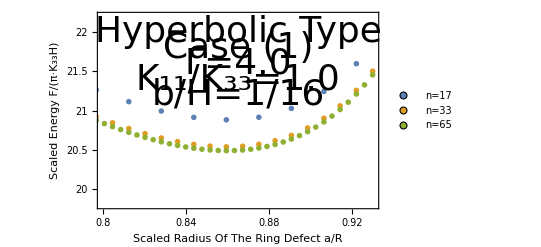

```mathematica
ListPlot[{b,b2,b3},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{20,20.5,21,21.5,22},None},{{0.8,0.82,0.84,0.86,0.88,0.90,0.92},None}}, PlotRange->{{0.8,0.93},{19.8,22.2}},FrameLabel->{{"Scaled Energy F/(π·K_33H)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"n=17","n=33","n=65"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["Hyperbolic Type",Directive[Black,36]],{0.865,22}],Text[Style["Case (1)",Directive[Black,36]],{0.865,21.8}],Text[Style["Γ=4.0",Directive[Black,36]],{0.865,21.6}],Text[Style["K_11/K_33=1.0",Directive[Black,36]],{0.865,21.4}],Text[Style["b/H=1/16",Directive[Black,36]],{0.865,21.2}]}]
```

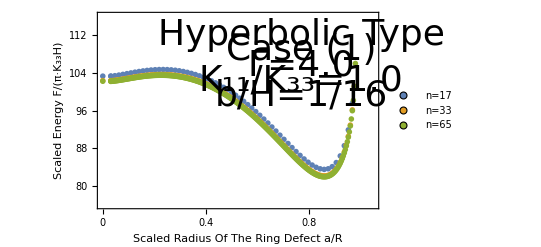

```mathematica
c=a*Table[{0.25,4},{i,0,62}];
c2=a2*Table[{0.25,4},{i,0,123}];
c3=a3*Table[{0.25,4},{i,0,245}];
ListPlot[{c,c2,c3},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{80,88,96,104,112},None},{{0,0.2,0.4,0.6,0.8,1.0},None}}, PlotRange->{{0,1.05},{76,116}},FrameLabel->{{"Scaled Energy F/(π·K_33H)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"n=17","n=33","n=65"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Bottom}],Epilog->{Inset[Graphics@{Red,Thickness[0.03],Dashing[0.1],Circle[{0,0},1]},{0.86,84},Center,Scaled[.25]],Text[Style["Hyperbolic Type",Directive[Black,36]],{0.77,112}],Text[Style["Case (1)",Directive[Black,36]],{0.77,108.8}],Text[Style["Γ=4.0",Directive[Black,36]],{0.77,105.6}],Text[Style["K_11/K_33=1.0",Directive[Black,36]],{0.77,102.4}],Text[Style["b/H=1/16",Directive[Black,36]],{0.77,99.2}]}]
```

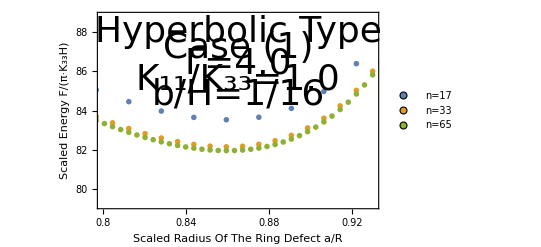

```mathematica
ListPlot[{c,c2,c3},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{80,82,84,86,88},None},{{0.8,0.82,0.84,0.86,0.88,0.90,0.92},None}}, PlotRange->{{0.8,0.93},{79.2,88.8}},FrameLabel->{{"Scaled Energy F/(π·K_33H)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"n=17","n=33","n=65"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["Hyperbolic Type",Directive[Black,36]],{0.865,88}],Text[Style["Case (1)",Directive[Black,36]],{0.865,87.2}],Text[Style["Γ=4.0",Directive[Black,36]],{0.865,86.4}],Text[Style["K_11/K_33=1.0",Directive[Black,36]],{0.865,85.6}],Text[Style["b/H=1/16",Directive[Black,36]],{0.865,84.8}]}]
```